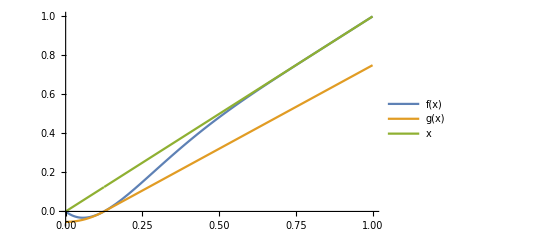

```mathematica
With[ {n = 7, k= 8},
g[x_] :=(n-1)/(k-1) (x-1/k)+(n-1)/(2(1-1/k))(x-1/k)^2 Boole[x<= 1/k];
f[x_] := x(1-((1-x)/(1-1/k))^(n-1));
p1 = Plot[{f[x],g[x],x},{x,0,1}, PlotLegends->"Expressions"];
Export["fig-uniformity-z2-fg.png",p1,ImageResolution->700];
Show[p1]]
```

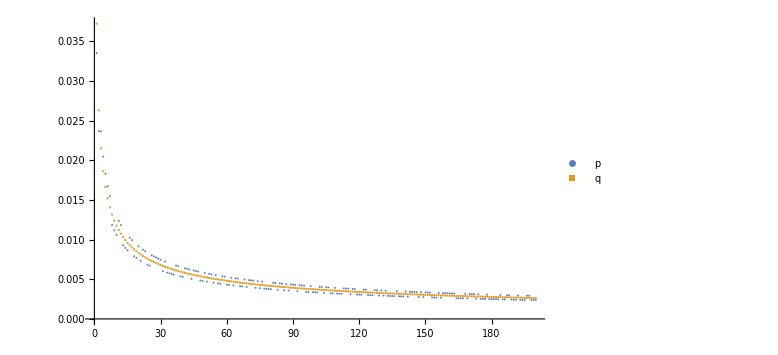

0.0372311

{-1,1,1,1,1,-1,-1,1,-1,1,-1,-1,-1,1,1,-1,-1,1,1,1,1,1,-1,1,1,-1,-1,-1,1,1,1,-1,-1,-1,1,1,1,1,1,1,-1,1,-1,-1,-1,-1,-1,1,-1,-1,-1,-1,1,1,1,1,-1,-1,-1,1,1,-1,-1,1,1,1,-1,1,1,1,1,-1,-1,-1,-1,1,-1,1,1,-1,-1,1,1,1,-1,1,1,-1,-1,1,1,1,1,-1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,1,1,1,-1,1,1,-1,-1,1,-1,-1,1,1,1,1,-1,1,1,1,1,-1,1,-1,1,-1,-1,1,-1,-1,1,1,-1,1,-1,-1,1,1,1,1,1,-1,1,-1,1,-1,-1,1,-1,-1,1,-1,1,-1,1,1,1,1,-1,-1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,-1,-1,1,1,-1,-1,1,-1,-1,1,1,-1,-1,1,1,1,1,-1,1,1,1,1,-1,-1}

1

```mathematica
With[{k=200,ϵ = 1/10}, 
perturb = 1+ ϵ (2 RandomVariate[BernoulliDistribution[1/2], k]-1);
zipf = Table[1/(HarmonicNumber[k,1/2]Sqrt[i]), {i,1,k}];

p2 = ListPlot[{ zipf*perturb,zipf}, PlotLegends->{"p", "q"}, PlotRange->Full, PlotMarkers->{Automatic, 2}, ImageSize->Large];
Export["fig-lowerbound-zipf-pq.png",p2,ImageResolution->1000];
Show[p2]]
```